```mathematica
b=Import["D:\\Programming\\ЧМ\\result_points.csv", "Data"];
```

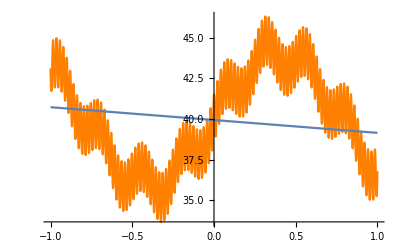

```mathematica
a=Import["D:\\Programming\\ЧМ\\result_points.csv", "Data"];
p1=Plot[1.5Cos@(300*x)+4Sin@(4*x)+Sin@(x*25)+(40-x*x/100),{x,-1,1},PlotStyle->{Orange}];
p2=ListLinePlot[a];
Show[p1, p2]
```

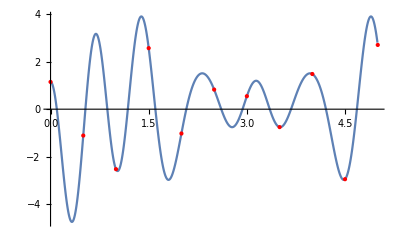

```mathematica
a=Import["D:\\Programming\\ЧМ\\init_points.csv", "Data"];
b=Import["D:\\Programming\\ЧМ\\result_points.csv", "Data"];
Show[ListLinePlot[b],ListPlot[a, PlotStyle->{Red,PointSize[Large]}]]
```

```mathematica
a
```

{{0,5.98472},{1,-3.15705},{2,-7.82024},{3,-4.93878},{4,1.29072},{5,4.69},{6,3.19395},{7,-0.225453},{8,-1.75939},{9,-0.875452},{10,0}}

```mathematica
g={Sqrt[1/Pi],x*Sqrt[2/Pi],(-1+2 x^2)*Sqrt[2/Pi],(4 x^3-3x)*Sqrt[2/Pi],(8 x^4-8 x^2+1)*Sqrt[2/Pi]}
Length@Tuples[g,2]
```

{1/(√π),√(2/π) x,√(2/π) (-1+2 x^2),√(2/π) (-3 x+4 x^3),√(2/π) (1-8 x^2+8 x^4)}

25

```mathematica
Map[Integrate[(#[[1]]*#[[2]])*1/Sqrt[1-x*x],{x,-1,1}]&,Tuples[g,2]]
```

{1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1}

```mathematica
f[x,Sqrt[2/Pi]]
```

1/2 (-√(2/π)+2 x^2)